```mathematica
On[Assert]
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/symbiosis_3D_tradeoff

# Graph format

```mathematica
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colfunctions = "ThermometerColors";
```

# Ecological dynamics of resident

```mathematica
dFdt = ρ F + τ A - α F^2- μ F - β F H; (*Free living parasites*)
dAdt = β H F + p r A - (ν + d)  A - γ(A + H)A; (*Association*)
dHdt = -β H F + r (1 - p)A + r  H - d H - γ(A + H)H; (*Free host*)
```

```mathematica
jacob = D[{dFdt, dAdt, dHdt}, {{F, A, H}}];
```

# Dynamics of mutants and invasion criteria

```mathematica
dFmdt = ρm Fm + τm Am - α F Fm- μ Fm - β Fm H; (*Free living parasites*)
dAmdt = β H Fm + p r Am - (νm + d)  Am - γ(A + H)Am; (*Association*) (*Free host*)
```

```mathematica
Mmat = {{ρm - α F - μ - β H, τm},{β H, r p - νm -d - γ(A + H)}};
Mmat . {Fm, Am} == {dFmdt, dAmdt}//Simplify//Assert
Fmat = {{ρm, τm}, {0, 0}};
Vmat = {{α F + μ + β H, 0}, {-β H, d-r p + νm + γ(A + H) }};
Fmat - Vmat == Mmat//Simplify//Assert
R0 = Eigenvalues[Fmat.Inverse[Vmat]][[2]];
```

```mathematica
ρm/(F α+H β+μ)+(H β τm)/((F α+H β+μ) (d-p r+A γ+H γ+νm))==R0//FullSimplify//Assert
```

## Tradeoff and Invasion surface

```mathematica
𝒪 = θ - v ρ^h + (η ν (ν + d)^g)/νmax; 
ℐ = ((d-p r+(A+H) γ+ν) (F α+H β+μ-ρ))/(H β);
```

```mathematica
jacobtroff = jacob/.τ-> 𝒪;
```

## Derivative of the invasion surface

```mathematica
dIdp = D[ℐ, ρ]/.ν-> νpoint;
dIdv = D[ℐ, ν]/.ρ-> ρpoint;
```

# Testing singular strategy

## Tradeoff parameterisation

```mathematica
parstroff = {θ -> 8, η -> 1, v -> 1., d-> 1.3, νmax -> 3};
𝒪/.parstroff
Manipulate[Plot3D[%, {ν, -1, 3}, {ρ, 0, 14}, AxesLabel->Automatic], {g, 0.1, 1.5}, {h, 0.1, 1.5}]
```

8+1/3 ν (1.3+ν)^g-1. ρ^h

## Equilibrium

```mathematica
system = Thread[({dFdt, dAdt, dHdt}/.τ-> 𝒪) ];
```

```mathematica
νeg = -0.05;
ρeg = 1.2;
parsTest =  { η -> 4.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4.52, h-> 0.382, νmax -> 3};
```

```mathematica
NSolvePositive[system,Join[ parsTest, {ν-> νeg, ρ-> ρeg}], τ-> 1, {F, A, H}, equi];
solTest = equi/.%[[1]][[2]]
```

{F→0.363533,A→0.224927,H→0.599176}

## Singular strategy

```mathematica
Show[Plot3D[ℐ/.parsTest/.solTest, {ν, -1, 3}, {ρ, 0, 4}, AxesLabel->{"ν", "ρ", "τ"}, Mesh -> None, PlotStyle->LightGray, Filling-> Top, AxesStyle->Directive[Black, 14]],
Graphics3D[{Black,PointSize[0.02],Point[{νeg,ρeg,𝒪/.parsTest/.ν -> νeg/.ρ-> ρeg}]}], Plot3D[ 𝒪/.parsTest , {ν, -1, 3}, {ρ, 0, 4}, AxesLabel->Automatic, Mesh-> Full, MeshStyle->{{Thick,Red}, {Thick,Red}}, PlotStyle->None]]
```

-Graphics3D-

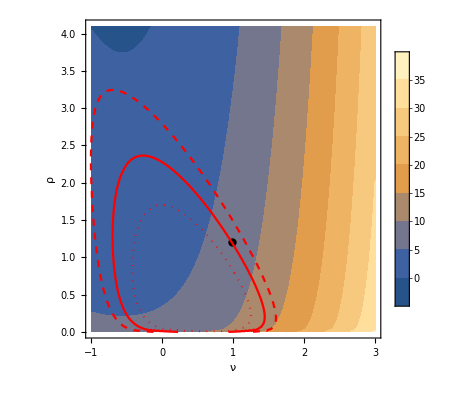

```mathematica
νeg =0.98;
ρeg = 1.2;
νrange = {-1, 3, 0.5};
ρrange = {0, 4.1, 0.5};
Show[ContourPlot[𝒪/.parsTest, {ν, νrange[[1]], νrange[[2]]}, {ρ,ρrange[[1]], ρrange[[2]]}, FrameLabel->Automatic, ContourStyle -> None,PlotLegends->Automatic],
Graphics[{PointSize[0.015],Point[{νeg, ρeg}]}],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==0, {ν, -3,3}, {ρ,0,4}, ContourStyle->Red ],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==0.2 * Round[Max[{Abs[dIdp/.parsTest/.solTest/.νpoint-> νeg],Abs[dIdv/.parsTest/.solTest/.ρpoint->ρeg]}], 0.01], {ν,-3,3}, {ρ,0,4}, ContourStyle->Directive[Red, Dashed] ],
ContourPlot[((𝒪-ℐ)/.parsTest/.solTest)==-0.2 * Round[Max[{Abs[dIdp/.parsTest/.solTest/.νpoint-> νeg],Abs[dIdv/.parsTest/.solTest/.ρpoint->ρeg]}], 0.01], {ν, -3,3}, {ρ, 0,4}, ContourStyle->Directive[Red, Dotted] ]]
```

```mathematica
R0troff = R0/.τm -> 𝒪/.ρ -> ρm /.ν-> νm;
R0troff/.parsTest/.solTest/.νm -> 0.1/.ρm -> 3
```

0.992234

```mathematica
Det[Mmat]/.solTest/.parsTest
```

8.08501+3.9058 νm-2.07 ρm-νm ρm-0.668728 τm

```mathematica
ℐ/.parsTest/.solTest/.ν-> 0./.ρ-> 3
```

2.80385

```mathematica
𝒪/.parsTest/.ν-> 0./.ρ-> 3
```

2.80385

```mathematica
Table[{{x, y}},  {x, -0.1, 0.1, 0.1}, {y, 2.9, 3.1, 0.1}]//TableForm
Table[R0troff/.parsTest/.νm ->x/. ρm->y/.solTest, {x, -0.1, 0.1, 0.1}, {y, 2.9, 3.1, 0.1}]//TableForm
```

-0.1 | 2.9 | -0.1 | 3. | -0.1 | 3.1
0. | 2.9 | 0. | 3. | 0. | 3.1
0.1 | 2.9 | 0.1 | 3. | 0.1 | 3.1

1.00549 | 1.00871 | 1.01154
0.995706 | 1. | 1.00394
0.986958 | 0.992234 | 0.997168

```mathematica
(ℐ - 𝒪)/.parsTest/.solTest/.ν ->0.1/. ρ->3
```

0.0984287

```mathematica
Show[Plot3D[R0troff/.parsTest/.solTest, {νm, -1, 3}, {ρm, 0, 4}, AxesLabel->Automatic, AspectRatio->1], Graphics3D[{Red,PointSize[0.02],Point[{νeg,ρeg,1}]}]]
```

-Graphics3D-

# Scenario 1 of the tradeoff plane: g < 1, h > 1, increase in ν does not cost a lot of energy

```mathematica
par1 = { η -> 1., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1., h-> 1.5, νmax -> 3};
νrange = {-1, 3, 0.5};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par1fullresult = Table[NSolveCodim2Positive[system, par1, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par1eq = eq/.Flatten[par1fullresult, 2];

par1νρ = νρ/.Flatten[par1fullresult, 2];
νlist =  par1νρ[[;;, 1]];
ρlist = par1νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.13, νlist+ 0.13}];
ρlistContourRange = Thread[{ρ, ρlist - 0.13, ρlist + 0.13}];
par1νρextinct = Complement[ νρlistfull, par1νρ];
Round[Max/@Transpose[{Abs[dIdp/.par1/.par1eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par1/.par1eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
PlotR
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par1, {ν, ρ}, par1νρ, par1eq];
Show[ContourPlot[𝒪/.par1, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par1/.par1eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par1/.par1eq)== 3 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par1/.par1eq)==-3*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par1νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par1νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par1) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 2 of the tradeoff plane: g < 1, h < 1, increase in both ν and ρ does not cost a lot of energy

```mathematica
par2 = { η -> 4., g ->  0.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4., h-> 0.382, νmax -> 3};
νrange = {-1, 3.1, 0.4};
ρrange = {0, 4.5, 0.5};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par2fullresult = Table[NSolveCodim2Positive[system, par2, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par2eq = eq/.Flatten[par2fullresult, 2];
par2νρ = νρ/.Flatten[par2fullresult, 2];
νlist =  par2νρ[[;;, 1]];
ρlist = par2νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.1, νlist+ 0.1}];
ρlistContourRange = Thread[{ρ, ρlist - 0.1, ρlist + 0.1}];
par2νρextinct = Complement[ νρlistfull, par2νρ];
Round[Max/@Transpose[{Abs[dIdp/.par2/.par2eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par2/.par2eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par2, {ν, ρ}, par2νρ, par2eq];
Show[ContourPlot[𝒪/.par2, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->"ThermometerColors",PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle, ContourStyle->Directive[Gray,Dashed]],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par2/.par2eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2/.par2eq)== 1.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪-ℐ)/.par2/.par2eq)==-1.9 * scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par2νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par2νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par2) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 3 of the tradeoff plane g > 1, h < 1, increase in ρ does not cost a lot of energy

```mathematica
par3 = { η -> 4.12, g ->  1.312, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 4.52, h-> 0.382, νmax -> 3};
νrange = {-1, 3, 0.3};
ρrange = {0, 4.1, 0.6};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par3fullresult = Table[NSolveCodim2Positive[system, par3, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par3eq = eq/.Flatten[par3fullresult, 2];
par3νρ = νρ/.Flatten[par3fullresult, 2];
νlist =  par3νρ[[;;, 1]];
ρlist = par3νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.12, νlist+ 0.12}];
ρlistContourRange = Thread[{ρ, ρlist - 0.12, ρlist + 0.12}];
par3νρextinct = Complement[ νρlistfull, par3νρ];
Round[Max/@Transpose[{Abs[dIdp/.par3/.par3eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par3/.par3eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par3, {ν, ρ}, par3νρ, par3eq];
Show[ContourPlot[𝒪/.par3, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪 - ℐ==0)/.par3/.par3eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3/.par3eq)==10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par3/.par3eq)==-10 *scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par3νρ, PlotStyle->Black, PlotMarkers-> markers],ListPlot[par3νρextinct, PlotStyle->Black, PlotMarkers->"X"],
RegionPlot[(𝒪/.par3) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-

# Scenario 4 of the tradeoff plane g > 1, h > 1, increase in both ρ and ν cost a lot of energy

```mathematica
par4 = { η -> 1.12, g ->  1.412, μ-> 1.4, α -> 1.2, γ -> 1.23, p-> 0.1, β -> 2.1, r -> 2.3, d -> 1.3, θ -> 8., v -> 1.32, h-> 1.582, νmax -> 3};
νrange = {-1, 3, 0.3};
ρrange = {0, 4.5, 0.7};
νρlistfull = Flatten[Table[{ν, ρ},{ν, νrange[[1]], νrange[[2]], νrange[[3]]}, {ρ, ρrange[[1]], ρrange[[2]], ρrange[[3]]}], 1];
par4fullresult = Table[NSolveCodim2Positive[system, par4, {ν-> νval}, {ρ-> ρval},νρ, eq, {F, A, H} ], {νval ,νrange[[1]], νrange[[2]], νrange[[3]]},{ρval,ρrange[[1]], ρrange[[2]], ρrange[[3]]}];
par4eq = eq/.Flatten[par4fullresult, 2];
par4νρ = νρ/.Flatten[par4fullresult, 2];
νlist =  par4νρ[[;;, 1]];
ρlist = par4νρ[[;;, 2]];
νlistContourRange =  Thread[{ν, νlist- 0.1, νlist+ 0.1}];
ρlistContourRange = Thread[{ρ, ρlist - 0.1, ρlist + 0.1}];
par4νρextinct = Complement[ νρlistfull, par4νρ];
Round[Max/@Transpose[{Abs[dIdp/.par4/.par4eq/.Thread[νpoint-> νlist]], Abs[dIdv/.par4/.par4eq/.Thread[ρpoint-> ρlist]]}], 0.01];
scale = %/Max[%];
```

```mathematica
markers = ListStableMarkTwoParameters[jacobtroff, par4, {ν, ρ}, par4νρ, par4eq];
Show[ContourPlot[𝒪/.par4, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]},Frame-> True, FrameLabel->{ "Effect on association's mortality (ν)","Independent Reproduction (ρ)"}, ColorFunction->colfunctions,ContourStyle -> None,PlotLegends->Automatic, FrameStyle->frameStyle, LabelStyle->labelStyle],MapThread[ContourPlot, {(𝒪-ℐ==0)/.par4/.par4eq, νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par4/.par4eq)==1.5*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dashed]}, Length[νlistContourRange]]}],
MapThread[ContourPlot, {Thread[((𝒪 - ℐ)/.par4/.par4eq)==-1.5*scale], νlistContourRange, ρlistContourRange, ConstantArray[{ ContourStyle->Directive[Black, Dotted]}, Length[νlistContourRange]]}],ListPlot[par4νρ, PlotStyle->Black, PlotMarkers->markers],ListPlot[par4νρextinct, PlotStyle->Black, PlotMarkers->"X"],RegionPlot[(𝒪/.par4) < 0, {ν, νrange[[1]], νrange[[2]]}, {ρ, ρrange[[1]], ρrange[[2]]}, PlotStyle->Black]]
```

-Graphics-